```mathematica
A={{3.3,1,2.1},{1,3.8,2.1},{2.1,2.1,4.4}}
f={2.1,1,1.1}
A==(A//Transpose)
Table[Det[A⟦1;;i,1;;i⟧],{i,1,3}]
```

{{3.3,1,2.1},{1,3.8,2.1},{2.1,2.1,4.4}}

{2.1,1,1.1}

True

{3.3,11.54,28.285}

```mathematica
x={}
y={}
```

{}

{}

```mathematica
L=DiagonalMatrix[{0,0,0},0]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
L⟦1,1⟧=Sqrt[A⟦1,1⟧];
L⟦2,1⟧=A⟦2,1⟧/L⟦1,1⟧;
L⟦3,1⟧=A⟦3,1⟧/L⟦1,1⟧;
L⟦2,2⟧=Sqrt[A⟦2,2⟧-L⟦2,1⟧^2];
L⟦3,2⟧=(A⟦3,2⟧-L⟦3,1⟧*L⟦2,1⟧)/L⟦2,2⟧;
L⟦3,3⟧=Sqrt[A⟦3,3⟧-L⟦3,1⟧^2-L⟦3,2⟧^2];
```

```mathematica
L.Transpose[L]//MatrixForm
```

(3.3 | 1. | 2.1
1. | 3.8 | 2.1
2.1 | 2.1 | 4.4)

```mathematica
AppendTo[y,f⟦1⟧/L⟦1,1⟧]
AppendTo[y,(f⟦2⟧-L⟦2,1⟧*y⟦1⟧)/L⟦2,2⟧]
AppendTo[y,(f⟦3⟧-L⟦3,1⟧*y⟦1⟧-L⟦3,2⟧*y⟦2⟧)/L⟦3,3⟧]
```

{1.15601}

{1.15601,0.194456}

{1.15601,0.194456,-0.24819}

```mathematica
LTransp=Transpose[L]
```

{{1.81659,0.550482,1.15601},{0,1.87002,0.782685},{0,0,1.56558}}

```mathematica
x={0,0,0}
```

{0,0,0}

```mathematica
x⟦3⟧=y⟦3⟧/L⟦3,3⟧
x⟦2⟧=(y⟦2⟧-L⟦3,2⟧*x⟦3⟧)/L⟦2,2⟧
x⟦1⟧=(y⟦1⟧-L⟦2,1⟧*x⟦2⟧-L⟦3,1⟧*x⟦3⟧)/L⟦1,1⟧
```

-0.158529

0.170338

0.685628

```mathematica
A.x-f
```

{-4.44089×10^-16,2.22045×10^-16,0.}

```mathematica
cubeNorm=Max[Abs[x.A-f]]
octNorm=Plus@@Abs[x.A-f]
Sqrt[Plus@@((x.A-f)*(x.A-f))]
```

4.44089×10^-16

6.66134×10^-16

4.96507×10^-16

```mathematica
ЛР4
```

ЛР4

```mathematica
A={{2,1,0.5},{0.5,5,0.72},{-0.3,-1,1.48}}
f={-2.9,-0.7,-12.06}
```

{{2,1,0.5},{0.5,5,0.72},{-0.3,-1,1.48}}

{-2.9,-0.7,-12.06}

```mathematica
{{2,1,0.5},{0.5,5,0.72},{-0.3,-1,1.48}}
```

{{2,1,0.5},{0.5,5,0.72},{-0.3,-1,1.48}}

```mathematica
A//MatrixForm
```

(2 | 1 | 0.5
0.5 | 5 | 0.72
-0.3 | -1 | 1.48)

```mathematica
mrxC={{1/2,0,0},{0,1/5,0},{0,0,1/1.48}}
mrxE={{1,0,0},{0,1,0},{0,0,1}}
B=mrxE-mrxC.A
mrxC//MatrixForm
B//MatrixForm
```

{{1/2,0,0},{0,1/5,0},{0,0,0.675676}}

{{1,0,0},{0,1,0},{0,0,1}}

{{0.,-0.5,-0.25},{-0.1,0.,-0.144},{0.202703,0.675676,0.}}

(1/2 | 0 | 0
0 | 1/5 | 0
0 | 0 | 0.675676)

(0. | -0.5 | -0.25
-0.1 | 0. | -0.144
0.202703 | 0.675676 | 0.)

```mathematica
cubeNormB=Max[Plus@@(B//Transpose)]
```

0.878378

```mathematica
g=mrxC.f
```

{-1.45,-0.14,-8.14865}

```mathematica
Max[Abs[mrxC.f]]
```

8.14865

```mathematica
x={}
```

{}

```mathematica
AppendTo[x,g]
AppendTo[x,B.g+g]
```

{{-1.45,-0.14,-8.14865}}

{{-1.45,-0.14,-8.14865},{0.657162,1.17841,-8.53716}}

```mathematica
ϵ=1/2*10^(-4)
```

1/20000

```mathematica
x
```

{{-1.45,-0.14,-8.14865},{0.657162,1.17841,-8.53716}}

```mathematica
For[i=2 ,Max[Abs[x⟦i⟧-x⟦i-1⟧]]>(1-cubeNormB)/cubeNormB*ϵ,i++,AppendTo[x,B.x⟦i⟧+g]]
```

```mathematica
x//MatrixForm
```

(-1.45 | -0.14 | -8.14865
0.657162 | 1.17841 | -8.53716
0.0950878 | 1.02364 | -7.21922
-0.157013 | 0.890059 | -7.43773
-0.0355973 | 0.946734 | -7.57908
-0.028596 | 0.954948 | -7.51618
-0.0484292 | 0.945189 | -7.50921
-0.0452922 | 0.946169 | -7.51982
-0.0431286 | 0.947384 | -7.51853
-0.0440604 | 0.946981 | -7.51727
-0.0441736 | 0.946892 | -7.51773
-0.0440142 | 0.94697 | -7.51781
-0.0440325 | 0.946966 | -7.51773
-0.0440516 | 0.946956 | -7.51773
-0.0440448 | 0.946959 | -7.51774
-0.0440435 | 0.946959 | -7.51774)

```mathematica
Max[Abs[x⟦-1⟧-x⟦-2⟧]]<(1-cubeNormB)/cubeNormB*ϵ
```

True

```mathematica
cubeNorm=Max[Abs[A.x⟦-1⟧-f]]
```

3.03043×10^-6

```mathematica
Bsymm={{p,q},{q,p}}
BAntisymm={{p,q},{-q,p}}
```

{{p,q},{q,p}}

{{p,q},{-q,p}}

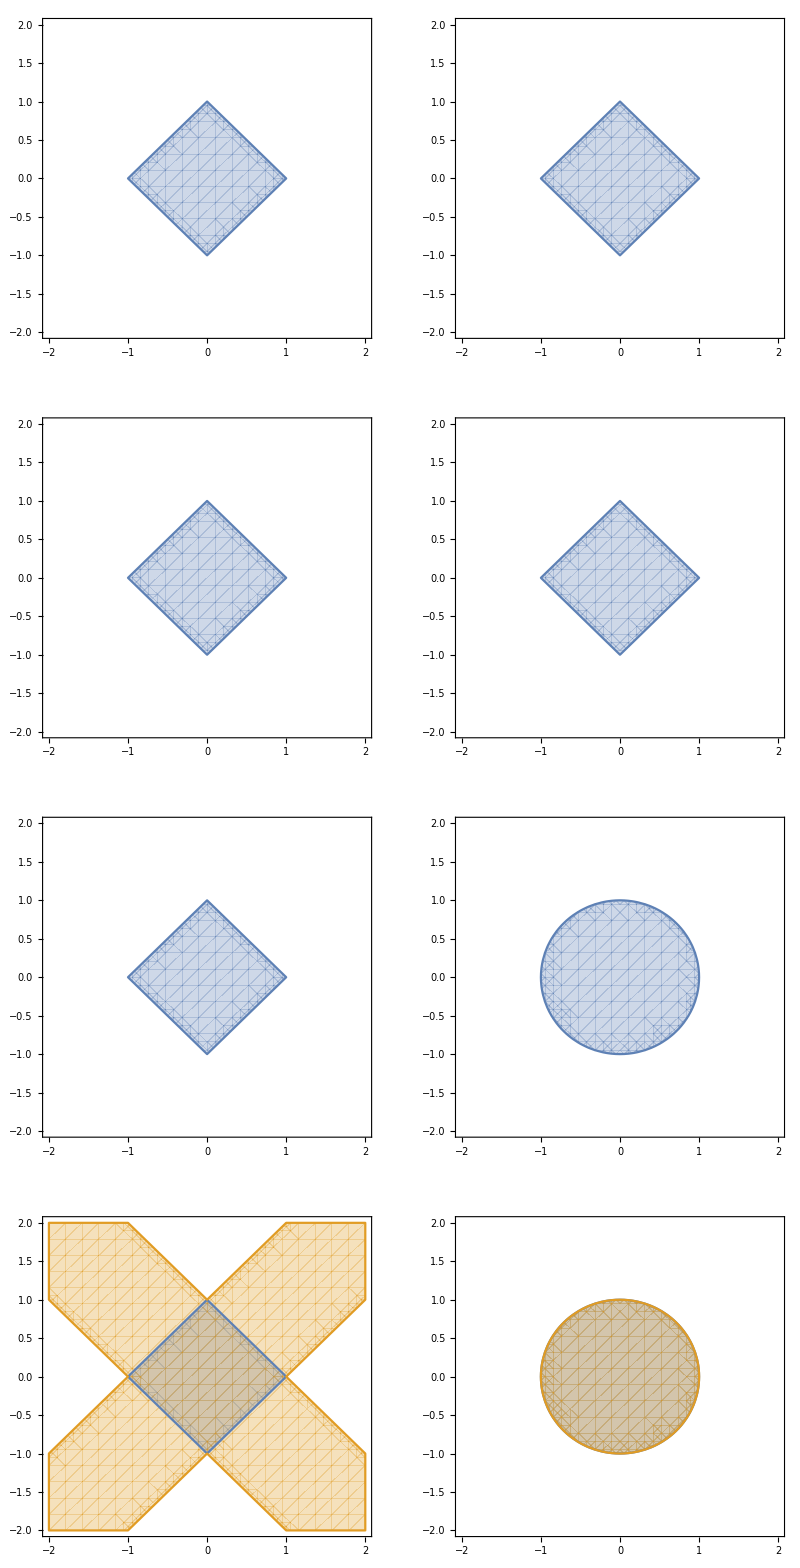

```mathematica
GraphicsGrid[{{RegionPlot[Max[Plus@@Abs[Bsymm//Transpose]]<1,{p,-2,2},{q,-2,2}],RegionPlot[Max[Plus@@Abs[BAntisymm//Transpose]]<1,{p,-2,2},{q,-2,2}]},
{RegionPlot[Max[Plus@@Abs[Bsymm]]<1,{p,-2,2},{q,-2,2}],RegionPlot[Max[Plus@@Abs[BAntisymm]]<1,{p,-2,2},{q,-2,2}]},
{RegionPlot[Norm[Bsymm]<1,{p,-2,2},{q,-2,2}],RegionPlot[Norm[BAntisymm]<1,{p,-2,2},{q,-2,2}]},
{RegionPlot[{Abs[Eigenvalues[Bsymm]]⟦1⟧<1 , Abs[Eigenvalues[Bsymm]]⟦2⟧<1},{p,-2,2},{q,-2,2}],RegionPlot[{Abs[Eigenvalues[BAntisymm]]⟦1⟧<1 , Abs[Eigenvalues[BAntisymm]]⟦2⟧<1 } ,{p,-2,2},{q,-2,2}]}}]
```

```mathematica
ЛР5
```

ЛР5

```mathematica
B//MatrixForm
```

(0. | -0.5 | -0.25
-0.1 | 0. | -0.144
0.202703 | 0.675676 | 0.)

```mathematica
F={{0,0,0},{-0.1,0,0},{0.202703,0.675676,0}}
H={{0,-0.5,-0.25},{0,0,-0.144},{0,0,0}}
```

{{0,0,0},{-0.1,0,0},{0.202703,0.675676,0}}

{{0,-0.5,-0.25},{0,0,-0.144},{0,0,0}}

```mathematica
F//MatrixForm
H//MatrixForm
```

(0 | 0 | 0
-0.1 | 0 | 0
0.202703 | 0.675676 | 0)

(0 | -0.5 | -0.25
0 | 0 | -0.144
0 | 0 | 0)

```mathematica
Emrx={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
B1=Inverse[(Emrx-F)].H
g1=Inverse[Emrx-F].g
```

{{0.,-0.5,-0.25},{0.,0.05,-0.119},{0.,-0.0675677,-0.131081}}

{-1.45,0.005,-8.43919}

```mathematica
B1//MatrixForm
```

(0. | -0.5 | -0.25
0. | 0.05 | -0.119
0. | -0.0675677 | -0.131081)

```mathematica
cubeNormB1=Max[Plus@@(Abs[B1//Transpose])]
(1-cubeNormB1)/cubeNormB1*ϵ
```

0.75

0.0000166667

```mathematica
xZeydel={}
AppendTo[xZeydel,g1]
AppendTo[xZeydel,B1.g1+g1]
```

{}

{{-1.45,0.005,-8.43919}}

{{-1.45,0.005,-8.43919},{0.657297,1.00951,-7.33331}}

```mathematica
For[i=2 ,Max[Abs[xZeydel⟦i⟧-xZeydel⟦i-1⟧]]>(1-cubeNormB1)/cubeNormB1*ϵ,i++,AppendTo[xZeydel,B1.xZeydel⟦i⟧+g1]]
```

```mathematica
xZeydel//MatrixForm
```

(-1.45 | 0.005 | -8.43919
0.657297 | 1.00951 | -7.33331
-0.12143 | 0.928139 | -7.54614
-0.0275344 | 0.949398 | -7.51274
-0.0465127 | 0.946487 | -7.51856
-0.0436036 | 0.947033 | -7.5176
-0.0441164 | 0.946946 | -7.51776
-0.0440324 | 0.946961 | -7.51774
-0.0440467 | 0.946959 | -7.51774)

```mathematica
cubeNormZeydel=Max[Abs[A.xZeydel⟦-1⟧-f]]
```

4.77189×10^-6

```mathematica
x⟦-1⟧
```

{-0.0440435,0.946959,-7.51774}

```mathematica
n=10
```

10

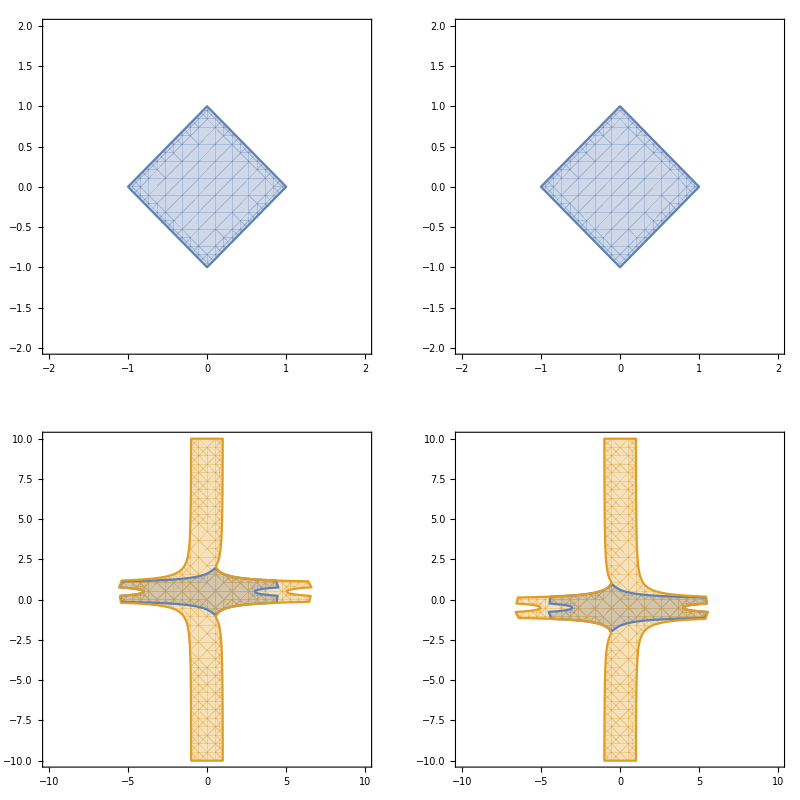

```mathematica
GraphicsGrid[{
{RegionPlot[Max[Plus@@Abs[Bsymm]]<1,{p,-2,2},{q,-2,2}],RegionPlot[Max[Plus@@Abs[BAntisymm]]<1,{p,-2,2},{q,-2,2}]},
{RegionPlot[{Abs[Eigenvalues[Reverse[E2x2-FBsymm].HB]⟦1⟧]<1 , Abs[Eigenvalues[Reverse[E2x2-FBsymm].HB]⟦2⟧]<1},{p,-n,n},{q,-n,n}],RegionPlot[{Abs[Eigenvalues[Reverse[E2x2-FBAntisymm].HB]]⟦1⟧<1 , Abs[Eigenvalues[Reverse[E2x2-FBAntisymm].HB]]⟦2⟧<1} ,{p,-n,n},{q,-n,n}]}
}]
```

```mathematica
FBsymm={{q,0},{0,0}}
FBAntisymm={{-q,0},{0,0}}
HB={{p,q},{0,q}}
E2x2={{1,0},{0,1}}
```

{{q,0},{0,0}}

{{-q,0},{0,0}}

{{p,q},{0,q}}

{{1,0},{0,1}}

```mathematica
Eigenvalues[Reverse[E2x2-FBsymm].HB]
Eigenvalues[Reverse[E2x2-FBAntisymm].HB]
```

{1/2 (q-q^2-√(4 p q+q^2-4 p q^2-2 q^3+q^4)),1/2 (q-q^2+√(4 p q+q^2-4 p q^2-2 q^3+q^4))}

{1/2 (q+q^2-√(q+q^2) √(4 p+q+q^2)),1/2 (q+q^2+√(q+q^2) √(4 p+q+q^2))}